## Import application packages

```mathematica
<<ProbabilisticBricks`
```

## Problem initialization

Set the geometry and other parameters using setProblemProperties[nelx, nely, b, h, P, μ], where nelx is the number of bricks per course, nely the number of courses, b and h are the dimensions of the brick, P is the weight of a brick and μ the static friction coefficient

```mathematica
setProblemProperties[30,50,2,1,0.1,0.7];
```

Generate random contacts

```mathematica
generateContacts[];
```

## Boundary conditions - Loads

Initialize the vector of loads acting on top of the wall in the form of {... N_1,V_1,N_2,V_2,N_3,V_3...} where every group of six components represents the loads on a brick ordered from left to right

```mathematica
p=Table[{0,0,1,0,0,0},{nelx}];
p[[4;;8]]={0,0,10,15,0,0};
p[[22;;26]]={0,0,10,-10,0,0};
p=Flatten[p];
setBoundaryConditions[p];
```

## Solution

Solve the problem and show the wall colored with the selected filter (“stress_state” or “contacts_state”)

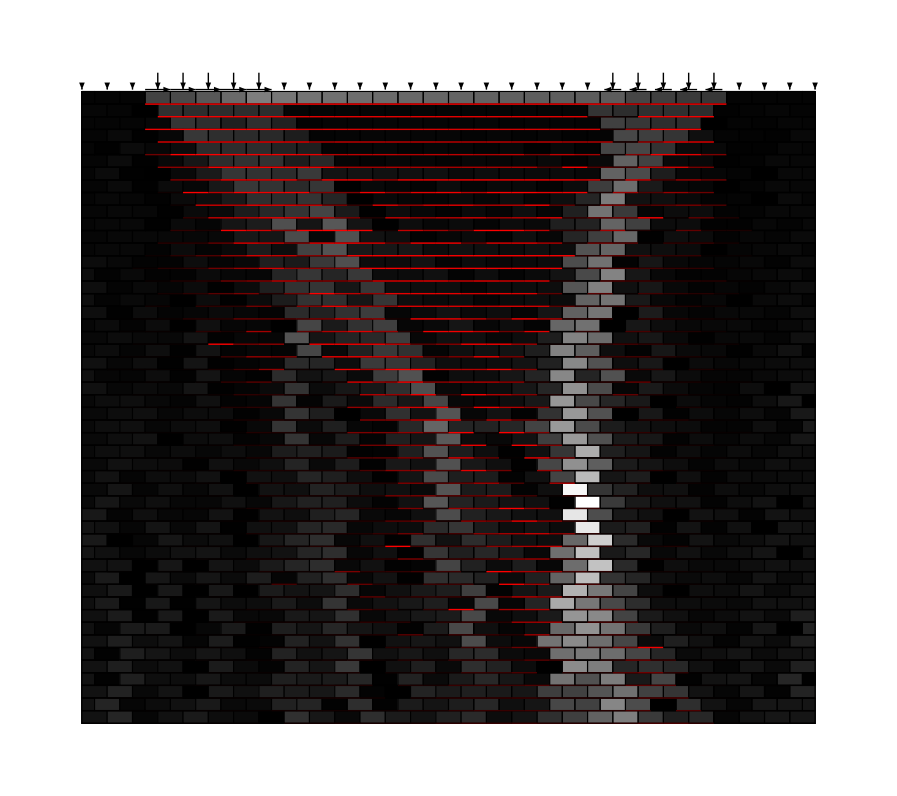

```mathematica
solveProblemAndDisplay["stress_state"]
```